# Erdos - Renyi curves

Graphs for some graph measurements for ensembles of Erdos-Renyi random graphs.

```mathematica
Get["/home/leo/thesis/graphs.m"];
```

## Play

```mathematica
n=100;p=0.4;
rann=Range[100,1000,100];
ranp=Range[0,1,0.01];
```

```mathematica
(*Do[graph[p]=newgraph[n,p],{p,ranp}]//AbsoluteTiming
Do[cluster[p]=gcc@graph@p,{p,ranp}]//AbsoluteTiming
Do[pathlen[p]=cpl@graph@p,{p,ranp}]//AbsoluteTiming*)
```

```mathematica
(*ListPlot[{
Thread[{ranp,pathlen/@ranp}],
Thread[{ranp,cluster/@ranp}]},ImageSize->Medium]*)
```

```mathematica
Do[graph[n,p]=newgraph[n,p],{p,ranp},{n,rann}]//AbsoluteTiming
Do[cluster[n,p]=gcc@graph[n,p],{p,ranp},{n,rann}]//AbsoluteTiming
Do[pathlen[n,p]=cpl@graph[n,p],{p,ranp},{n,rann}]//AbsoluteTiming
```

{5.29624,Null}

{50.79104,Null}

{249.56367,Null}

```mathematica
ListPlot3D[{
Flatten[Table[{n,p,cluster[n,p]},{p,ranp},{n,rann}],1],
Flatten[Table[{n,p,pathlen[n,p]},{p,ranp},{n,rann}],1]}]
```

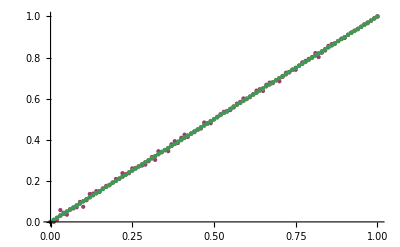

```mathematica
ListPlot[{
Thread[{ranp,Table[p,{p,ranp}]}],
Thread[{ranp,Table[cluster[100,p],{p,ranp}]}],
Thread[{ranp,Table[cluster[500,p],{p,ranp}]}],
Thread[{ranp,Table[cluster[1000,p],{p,ranp}]}]
}
]
```

## Play

```mathematica
(*prob[1]:=p*)
prob[l_]:=(1-(1-p^l)^Binomial[-2+n,-1+l]) ∏_(r=1)^(-1+l) (1-p^r)^Binomial[-2+n,-1+r]
```

```mathematica
Sum[l prob[l],{l,1,n-1}]
```

∑_(l=1)^(-1+n) l (1-(1-p^l)^Binomial[-2+n,-1+l]) ∏_(r=1)^(-1+l) (1-p^r)^Binomial[-2+n,-1+r]

```mathematica
Block[{p=0.4,n=100},Sum[l prob[l],{l,1,n-1}]]
```